```mathematica
SetDirectory[NotebookDirectory[]];
Remove["Global`*"]//Quiet;
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"lib_v_2.nb"}],InsertResults->False];
```

# Teoria gier

## Gry symetryczne

Definicja. (Totally symmetric) Gra w postaci normalnej jest symetryczna (całkowicie symetryczna) jeżeli dla dowolnej permutacji π, na zbiorze {1,…,I}, zachodzi u_i(a_1,…,a_I)=u_(π(i))(a_(π(1)),…,a_(π(I))).

Uwaga. Powyższa definicja jest czasem podawana w następujący sposób. Gra w postaci normalnej jest symetryczna jeżeli gracze mają identyczne przestrzenie strategii, tj. S_1=…=S_I oraz zachodzi u_i(s_i,s_-i)=u_j(s_j,s_-j) dla s_i=s_j i s_-i=s_-j dla wszystkich i,j∈ℐ. W szczególności, oznacza to, że wypłata dowolnego gracza grającego strategię t w profilu s jest zawsze zadana jako u(t,s).

Uwaga. W przypadku gier symetrycznych naturalnym pytaniem jest pytanie o symetryczne równowagi Nash. Okazuje się, że istnienie symetrycznych równowag Nasha dla gier symetrycznych jest gwarantowane.

Twierdzenie. W symetrycznej skończonej grze w postaci normalnej, gdzie liczba strategii wynosi 2 (dla każdego gracza) zawsze istnieje równowaga Nasha w strategiach czystych.

Uwaga. Z powyższego twierdzenia wynika, że dla gier symetrycznych z dwoma strategiami znalezienie przynajmniej jednej równowagi Nasha jest relatywnie proste.

Twierdzenie. W symetrycznej skończonej grze w postaci normalnej, zawsze istnieje symetryczna równowaga Nasha być może w strategiach mieszanych.

## Co dokładnie oznacza symetria gier?

Uwaga. Aby lepiej zrozumieć co tak naprawdę oznacza symetria możemy posłużyć się następującymi przykładami. W pierwszej kolejności chcemy mieć zrozumiałą notacją dla wypłat graczy. Poniższy kod tworzy odpowiednie formatownia.

```mathematica
Format[u[i_][s___]]:=Subscript[u, i][MapAt[Framed[#,Background->LightMagenta]&,{s},i]/.List->Sequence]
```

Przy powyższych formatowania np. wyrażenie u_2(a,b,c) jest formatowany w następujący sposób.

```mathematica
u[2][1,2,3]
```

u_2[1,2,3]

Następnie chcemy naśladować definicję. W tym celu musimy wiedzieć jak wygląda zastosowanie permutacji do danej wypłaty. Poniższa funkcja implementuje taką funkcjonalności.

```mathematica
ClearAll[applyPerm]
applyPerm[perm_,payoff_]:=u[perm⟦First@Head[payoff]⟧][((payoff/.Head[payoff]->List)⟦perm⟧)/.List->Sequence]
```

Przykładowe wykorzystanie.

```mathematica
applyPerm[{2,1,3},u[1][1,2,3]]
```

u_2[2,1,3]

W powyższym przykładzie zamieniliśmy miejscami gracza pierwszego i drugiego, zgodnie z definicją wypłata pierwszego gracza grającego pierwszą akcję przeciwko dwóm pozostałym graczom grającym akcje drugą i trzecią odpowiednio, musi być równa wypłacie gracza drugiego, który gra pierwszą akcję przeciwko graczom pierwszemu i trzeciemu grającym odpowiednio drugą i trzecią akcję.

W szczególności widzimy, że wypłata gracza i tego nie może zależeć od kolejności tego co grają pozostali gracze.

```mathematica
applyPerm[{1,3,2},u[1][1,2,3]]
```

u_1[1,3,2]

Uwaga. W szczególności wszystkie równości dla gry dwuosobowej z dwoma akcjami wyglądają następująco.

```mathematica
g=Table[
u[1][i,j],
{i,1,3,1},
{j,1,3,1}
];
gFlat=Flatten[g,1];
MatrixForm[g]
```

(u_1[1,1] | u_1[1,2] | u_1[1,3]
u_1[2,1] | u_1[2,2] | u_1[2,3]
u_1[3,1] | u_1[3,2] | u_1[3,3])

Zastosowanie identyczności oczywiście nie generuje żadnych interesujących wyników.

```mathematica
gFlat
```

{u_1[1,1],u_1[1,2],u_1[1,3],u_1[2,1],u_1[2,2],u_1[2,3],u_1[3,1],u_1[3,2],u_1[3,3]}

```mathematica
applyPerm[{1,2},#]&/@gFlat
```

{u_1[1,1],u_1[1,2],u_1[1,3],u_1[2,1],u_1[2,2],u_1[2,3],u_1[3,1],u_1[3,2],u_1[3,3]}

```mathematica
Thread[Evaluate[applyPerm[{1,2},#]&/@gFlat]==gFlat]
```

True

Transpozycja jest znacznie bardziej interesująca bo zadaje warunki na równości pomiędzy kolejnymi wypłatami pomiędzy graczami.

```mathematica
res=applyPerm[{2,1},#]&/@gFlat
```

{u_2[1,1],u_2[2,1],u_2[3,1],u_2[1,2],u_2[2,2],u_2[3,2],u_2[1,3],u_2[2,3],u_2[3,3]}

```mathematica
subs=Thread[res->gFlat];
Column[subs]
```

u_2[1,1]→u_1[1,1]
u_2[2,1]→u_1[1,2]
u_2[3,1]→u_1[1,3]
u_2[1,2]→u_1[2,1]
u_2[2,2]→u_1[2,2]
u_2[3,2]→u_1[2,3]
u_2[1,3]→u_1[3,1]
u_2[2,3]→u_1[3,2]
u_2[3,3]→u_1[3,3]

```mathematica
h=Table[
u[2][i,j],
{i,1,3,1},
{j,1,3,1}
];
```

```mathematica
MatrixForm[h]
```

(u_2[1,1] | u_2[1,2] | u_2[1,3]
u_2[2,1] | u_2[2,2] | u_2[2,3]
u_2[3,1] | u_2[3,2] | u_2[3,3])

```mathematica
h/.subs//MatrixForm
```

(u_1[1,1] | u_1[2,1] | u_1[3,1]
u_1[1,2] | u_1[2,2] | u_1[3,2]
u_1[1,3] | u_1[2,3] | u_1[3,3])

Jak widać jest to prosta transpozycja macierzy.

Uwaga. Dla gry z trzema graczami, gdzie każdy ma dwie akcje, powyższe ćwiczenie wygląda w następujący sposób. Tensor wypłat dla pierwszego gracza jest ogólnie następującej postaci.

```mathematica
g=Table[u[1][i,j,k],{i,1,2},{j,1,2},{k,1,2}];
MatrixForm[g,TableHeadings->{Range[2],Range[2]}]
```

( | 1 | 2
1 | (u_1[1,1,1]
u_1[1,1,2]) | (u_1[1,2,1]
u_1[1,2,2])
2 | (u_1[2,1,1]
u_1[2,1,2]) | (u_1[2,2,1]
u_1[2,2,2]))

```mathematica
gFlat=Flatten[Table[u[l][i,j,k],{l,1,3,1},{i,1,2},{j,1,2},{k,1,2}],3]
```

{u_1[1,1,1],u_1[1,1,2],u_1[1,2,1],u_1[1,2,2],u_1[2,1,1],u_1[2,1,2],u_1[2,2,1],u_1[2,2,2],u_2[1,1,1],u_2[1,1,2],u_2[1,2,1],u_2[1,2,2],u_2[2,1,1],u_2[2,1,2],u_2[2,2,1],u_2[2,2,2],u_3[1,1,1],u_3[1,1,2],u_3[1,2,1],u_3[1,2,2],u_3[2,1,1],u_3[2,1,2],u_3[2,2,1],u_3[2,2,2]}

Jakie symmetrie muszą występować w takiej grze? Musimy sprawdzić jak wyglądają symetrie wynikające z kolejnych permutacji. W pierwszej kolejności tworzymy wszystkie możliwe permutacje zbioru trzech elementów (mamy trzech graczy).

```mathematica
perms=Rest@Permutations[Range[3]]
```

{{1,3,2},{2,1,3},{2,3,1},{3,1,2},{3,2,1}}

W następnej kolejności stosujemy wszystkie permutacje do wszystkich wypłat pierwszego gracza drugiego gracza itd. To zadaje nam wszystkie zależności, które muszą być spełnione w grze symetrycznej.

```mathematica
conds=Flatten[Function[{p},Thread[Evaluate[applyPerm[p,#]&/@gFlat]==gFlat]]/@perms,1]
```

{True,u_1[1,2,1]==u_1[1,1,2],u_1[1,1,2]==u_1[1,2,1],True,True,u_1[2,2,1]==u_1[2,1,2],u_1[2,1,2]==u_1[2,2,1],True,u_3[1,1,1]==u_2[1,1,1],u_3[1,2,1]==u_2[1,1,2],u_3[1,1,2]==u_2[1,2,1],u_3[1,2,2]==u_2[1,2,2],u_3[2,1,1]==u_2[2,1,1],u_3[2,2,1]==u_2[2,1,2],u_3[2,1,2]==u_2[2,2,1],u_3[2,2,2]==u_2[2,2,2],u_2[1,1,1]==u_3[1,1,1],u_2[1,2,1]==u_3[1,1,2],u_2[1,1,2]==u_3[1,2,1],u_2[1,2,2]==u_3[1,2,2],u_2[2,1,1]==u_3[2,1,1],u_2[2,2,1]==u_3[2,1,2],u_2[2,1,2]==u_3[2,2,1],u_2[2,2,2]==u_3[2,2,2],u_2[1,1,1]==u_1[1,1,1],u_2[1,1,2]==u_1[1,1,2],u_2[2,1,1]==u_1[1,2,1],u_2[2,1,2]==u_1[1,2,2],u_2[1,2,1]==u_1[2,1,1],u_2[1,2,2]==u_1[2,1,2],u_2[2,2,1]==u_1[2,2,1],u_2[2,2,2]==u_1[2,2,2],u_1[1,1,1]==u_2[1,1,1],u_1[1,1,2]==u_2[1,1,2],u_1[2,1,1]==u_2[1,2,1],u_1[2,1,2]==u_2[1,2,2],u_1[1,2,1]==u_2[2,1,1],u_1[1,2,2]==u_2[2,1,2],u_1[2,2,1]==u_2[2,2,1],u_1[2,2,2]==u_2[2,2,2],True,True,u_3[2,1,1]==u_3[1,2,1],u_3[2,1,2]==u_3[1,2,2],u_3[1,2,1]==u_3[2,1,1],u_3[1,2,2]==u_3[2,1,2],True,True,u_2[1,1,1]==u_1[1,1,1],u_2[1,2,1]==u_1[1,1,2],u_2[2,1,1]==u_1[1,2,1],u_2[2,2,1]==u_1[1,2,2],u_2[1,1,2]==u_1[2,1,1],u_2[1,2,2]==u_1[2,1,2],u_2[2,1,2]==u_1[2,2,1],u_2[2,2,2]==u_1[2,2,2],u_3[1,1,1]==u_2[1,1,1],u_3[1,2,1]==u_2[1,1,2],u_3[2,1,1]==u_2[1,2,1],u_3[2,2,1]==u_2[1,2,2],u_3[1,1,2]==u_2[2,1,1],u_3[1,2,2]==u_2[2,1,2],u_3[2,1,2]==u_2[2,2,1],u_3[2,2,2]==u_2[2,2,2],u_1[1,1,1]==u_3[1,1,1],u_1[1,2,1]==u_3[1,1,2],u_1[2,1,1]==u_3[1,2,1],u_1[2,2,1]==u_3[1,2,2],u_1[1,1,2]==u_3[2,1,1],u_1[1,2,2]==u_3[2,1,2],u_1[2,1,2]==u_3[2,2,1],u_1[2,2,2]==u_3[2,2,2],u_3[1,1,1]==u_1[1,1,1],u_3[2,1,1]==u_1[1,1,2],u_3[1,1,2]==u_1[1,2,1],u_3[2,1,2]==u_1[1,2,2],u_3[1,2,1]==u_1[2,1,1],u_3[2,2,1]==u_1[2,1,2],u_3[1,2,2]==u_1[2,2,1],u_3[2,2,2]==u_1[2,2,2],u_1[1,1,1]==u_2[1,1,1],u_1[2,1,1]==u_2[1,1,2],u_1[1,1,2]==u_2[1,2,1],u_1[2,1,2]==u_2[1,2,2],u_1[1,2,1]==u_2[2,1,1],u_1[2,2,1]==u_2[2,1,2],u_1[1,2,2]==u_2[2,2,1],u_1[2,2,2]==u_2[2,2,2],u_2[1,1,1]==u_3[1,1,1],u_2[2,1,1]==u_3[1,1,2],u_2[1,1,2]==u_3[1,2,1],u_2[2,1,2]==u_3[1,2,2],u_2[1,2,1]==u_3[2,1,1],u_2[2,2,1]==u_3[2,1,2],u_2[1,2,2]==u_3[2,2,1],u_2[2,2,2]==u_3[2,2,2],u_3[1,1,1]==u_1[1,1,1],u_3[2,1,1]==u_1[1,1,2],u_3[1,2,1]==u_1[1,2,1],u_3[2,2,1]==u_1[1,2,2],u_3[1,1,2]==u_1[2,1,1],u_3[2,1,2]==u_1[2,1,2],u_3[1,2,2]==u_1[2,2,1],u_3[2,2,2]==u_1[2,2,2],True,u_2[2,1,1]==u_2[1,1,2],True,u_2[2,2,1]==u_2[1,2,2],u_2[1,1,2]==u_2[2,1,1],True,u_2[1,2,2]==u_2[2,2,1],True,u_1[1,1,1]==u_3[1,1,1],u_1[2,1,1]==u_3[1,1,2],u_1[1,2,1]==u_3[1,2,1],u_1[2,2,1]==u_3[1,2,2],u_1[1,1,2]==u_3[2,1,1],u_1[2,1,2]==u_3[2,1,2],u_1[1,2,2]==u_3[2,2,1],u_1[2,2,2]==u_3[2,2,2]}

W powyższych warunkach wiele jest trywialnie spełnionych i wiele się powtarza. Chcemy usunąć te powtarzające się warunki.

```mathematica
conds=DeleteDuplicates[conds]
```

{True,u_1[1,2,1]==u_1[1,1,2],u_1[1,1,2]==u_1[1,2,1],u_1[2,2,1]==u_1[2,1,2],u_1[2,1,2]==u_1[2,2,1],u_3[1,1,1]==u_2[1,1,1],u_3[1,2,1]==u_2[1,1,2],u_3[1,1,2]==u_2[1,2,1],u_3[1,2,2]==u_2[1,2,2],u_3[2,1,1]==u_2[2,1,1],u_3[2,2,1]==u_2[2,1,2],u_3[2,1,2]==u_2[2,2,1],u_3[2,2,2]==u_2[2,2,2],u_2[1,1,1]==u_3[1,1,1],u_2[1,2,1]==u_3[1,1,2],u_2[1,1,2]==u_3[1,2,1],u_2[1,2,2]==u_3[1,2,2],u_2[2,1,1]==u_3[2,1,1],u_2[2,2,1]==u_3[2,1,2],u_2[2,1,2]==u_3[2,2,1],u_2[2,2,2]==u_3[2,2,2],u_2[1,1,1]==u_1[1,1,1],u_2[1,1,2]==u_1[1,1,2],u_2[2,1,1]==u_1[1,2,1],u_2[2,1,2]==u_1[1,2,2],u_2[1,2,1]==u_1[2,1,1],u_2[1,2,2]==u_1[2,1,2],u_2[2,2,1]==u_1[2,2,1],u_2[2,2,2]==u_1[2,2,2],u_1[1,1,1]==u_2[1,1,1],u_1[1,1,2]==u_2[1,1,2],u_1[2,1,1]==u_2[1,2,1],u_1[2,1,2]==u_2[1,2,2],u_1[1,2,1]==u_2[2,1,1],u_1[1,2,2]==u_2[2,1,2],u_1[2,2,1]==u_2[2,2,1],u_1[2,2,2]==u_2[2,2,2],u_3[2,1,1]==u_3[1,2,1],u_3[2,1,2]==u_3[1,2,2],u_3[1,2,1]==u_3[2,1,1],u_3[1,2,2]==u_3[2,1,2],u_2[1,2,1]==u_1[1,1,2],u_2[2,2,1]==u_1[1,2,2],u_2[1,1,2]==u_1[2,1,1],u_2[2,1,2]==u_1[2,2,1],u_3[2,1,1]==u_2[1,2,1],u_3[2,2,1]==u_2[1,2,2],u_3[1,1,2]==u_2[2,1,1],u_3[1,2,2]==u_2[2,1,2],u_1[1,1,1]==u_3[1,1,1],u_1[1,2,1]==u_3[1,1,2],u_1[2,1,1]==u_3[1,2,1],u_1[2,2,1]==u_3[1,2,2],u_1[1,1,2]==u_3[2,1,1],u_1[1,2,2]==u_3[2,1,2],u_1[2,1,2]==u_3[2,2,1],u_1[2,2,2]==u_3[2,2,2],u_3[1,1,1]==u_1[1,1,1],u_3[2,1,1]==u_1[1,1,2],u_3[1,1,2]==u_1[1,2,1],u_3[2,1,2]==u_1[1,2,2],u_3[1,2,1]==u_1[2,1,1],u_3[2,2,1]==u_1[2,1,2],u_3[1,2,2]==u_1[2,2,1],u_3[2,2,2]==u_1[2,2,2],u_1[2,1,1]==u_2[1,1,2],u_1[1,1,2]==u_2[1,2,1],u_1[2,2,1]==u_2[2,1,2],u_1[1,2,2]==u_2[2,2,1],u_2[2,1,1]==u_3[1,1,2],u_2[2,1,2]==u_3[1,2,2],u_2[1,2,1]==u_3[2,1,1],u_2[1,2,2]==u_3[2,2,1],u_3[1,2,1]==u_1[1,2,1],u_3[2,2,1]==u_1[1,2,2],u_3[1,1,2]==u_1[2,1,1],u_3[2,1,2]==u_1[2,1,2],u_2[2,1,1]==u_2[1,1,2],u_2[2,2,1]==u_2[1,2,2],u_2[1,1,2]==u_2[2,1,1],u_2[1,2,2]==u_2[2,2,1],u_1[2,1,1]==u_3[1,1,2],u_1[1,2,1]==u_3[1,2,1],u_1[2,1,2]==u_3[2,1,2],u_1[1,2,2]==u_3[2,2,1]}

Korzystając z powyższych warunków wynikających z zastosowania pojedynczych permutacji do dowolnych wypłat, możemy dowodzić różnych równości w grach symetrycznych. Poniżej jest kilka przykładów takich zależności. W pierwszej kolejności możemy zweryfikować, że kolejność w jakiej przeciwnicy grają swoje strategie jest bez znaczenia w grach symetrycznych.

```mathematica
FindEquationalProof[u[1][2,1,2]==u[1][2,2,1],conds]
```

ProofObject[…]

```mathematica
FindEquationalProof[u[3][2,1,1]==u[3][1,2,1],conds]
```

ProofObject[…]

Ciekawe jest, że nie są to jedyne symetrie, które muszą występować w grze symetrycznej. W szczególności musimy mieć następujące zależności.

```mathematica
FindEquationalProof[u[1][2,1,2]==u[1][1,2,2],conds]
```

ProofObject[…]

```mathematica
FindEquationalProof[u[1][2,2,1]==u[1][1,2,2],conds]
```

ProofObject[…]

```mathematica
FindEquationalProof[u[1][1,2,1]==u[1][2,1,1],conds]
```

ProofObject[…]

```mathematica
FindEquationalProof[u[1][1,1,2]==u[1][2,1,1],conds]
```

ProofObject[…]

Chcemy wizualnie przedstawić równości, które muszą występować w grach symetrycznych.

```mathematica
profiles=Flatten[Outer[List,Range[2],Range[2],Range[2]],2]
```

{{1,1,1},{1,1,2},{1,2,1},{1,2,2},{2,1,1},{2,1,2},{2,2,1},{2,2,2}}

```mathematica
fig0=ListPointPlot3D[
(Callout[#,ToString[#]])&/@profiles,
BoxRatios->{1,1,1},
AxesLabel->{"player 1","player 2","player 3"},
SphericalRegion->True,
Axes->True,
Ticks->{{1,2},{1,2},{1,2}}
]
```

-Graphics3D-

```mathematica
payoffs=u[1][#/.List->Sequence]&/@profiles
```

{u_1[1,1,1],u_1[1,1,2],u_1[1,2,1],u_1[1,2,2],u_1[2,1,1],u_1[2,1,2],u_1[2,2,1],u_1[2,2,2]}

```mathematica
tests=Rest@DeleteDuplicates[Flatten[Outer[Equal,payoffs,payoffs]]]
```

{u_1[1,1,1]==u_1[1,1,2],u_1[1,1,1]==u_1[1,2,1],u_1[1,1,1]==u_1[1,2,2],u_1[1,1,1]==u_1[2,1,1],u_1[1,1,1]==u_1[2,1,2],u_1[1,1,1]==u_1[2,2,1],u_1[1,1,1]==u_1[2,2,2],u_1[1,1,2]==u_1[1,1,1],u_1[1,1,2]==u_1[1,2,1],u_1[1,1,2]==u_1[1,2,2],u_1[1,1,2]==u_1[2,1,1],u_1[1,1,2]==u_1[2,1,2],u_1[1,1,2]==u_1[2,2,1],u_1[1,1,2]==u_1[2,2,2],u_1[1,2,1]==u_1[1,1,1],u_1[1,2,1]==u_1[1,1,2],u_1[1,2,1]==u_1[1,2,2],u_1[1,2,1]==u_1[2,1,1],u_1[1,2,1]==u_1[2,1,2],u_1[1,2,1]==u_1[2,2,1],u_1[1,2,1]==u_1[2,2,2],u_1[1,2,2]==u_1[1,1,1],u_1[1,2,2]==u_1[1,1,2],u_1[1,2,2]==u_1[1,2,1],u_1[1,2,2]==u_1[2,1,1],u_1[1,2,2]==u_1[2,1,2],u_1[1,2,2]==u_1[2,2,1],u_1[1,2,2]==u_1[2,2,2],u_1[2,1,1]==u_1[1,1,1],u_1[2,1,1]==u_1[1,1,2],u_1[2,1,1]==u_1[1,2,1],u_1[2,1,1]==u_1[1,2,2],u_1[2,1,1]==u_1[2,1,2],u_1[2,1,1]==u_1[2,2,1],u_1[2,1,1]==u_1[2,2,2],u_1[2,1,2]==u_1[1,1,1],u_1[2,1,2]==u_1[1,1,2],u_1[2,1,2]==u_1[1,2,1],u_1[2,1,2]==u_1[1,2,2],u_1[2,1,2]==u_1[2,1,1],u_1[2,1,2]==u_1[2,2,1],u_1[2,1,2]==u_1[2,2,2],u_1[2,2,1]==u_1[1,1,1],u_1[2,2,1]==u_1[1,1,2],u_1[2,2,1]==u_1[1,2,1],u_1[2,2,1]==u_1[1,2,2],u_1[2,2,1]==u_1[2,1,1],u_1[2,2,1]==u_1[2,1,2],u_1[2,2,1]==u_1[2,2,2],u_1[2,2,2]==u_1[1,1,1],u_1[2,2,2]==u_1[1,1,2],u_1[2,2,2]==u_1[1,2,1],u_1[2,2,2]==u_1[1,2,2],u_1[2,2,2]==u_1[2,1,1],u_1[2,2,2]==u_1[2,1,2],u_1[2,2,2]==u_1[2,2,1]}

```mathematica
proofs={#,FindEquationalProof[#,conds]}&/@tests
```

{{u_1[1,1,1]==u_1[1,1,2],Failure[…]},{u_1[1,1,1]==u_1[1,2,1],Failure[…]},{u_1[1,1,1]==u_1[1,2,2],Failure[…]},{u_1[1,1,1]==u_1[2,1,1],Failure[…]},{u_1[1,1,1]==u_1[2,1,2],Failure[…]},{u_1[1,1,1]==u_1[2,2,1],Failure[…]},{u_1[1,1,1]==u_1[2,2,2],Failure[…]},{u_1[1,1,2]==u_1[1,1,1],Failure[…]},{u_1[1,1,2]==u_1[1,2,1],ProofObject[…]},{u_1[1,1,2]==u_1[1,2,2],Failure[…]},{u_1[1,1,2]==u_1[2,1,1],ProofObject[…]},{u_1[1,1,2]==u_1[2,1,2],Failure[…]},{u_1[1,1,2]==u_1[2,2,1],Failure[…]},{u_1[1,1,2]==u_1[2,2,2],Failure[…]},{u_1[1,2,1]==u_1[1,1,1],Failure[…]},{u_1[1,2,1]==u_1[1,1,2],ProofObject[…]},{u_1[1,2,1]==u_1[1,2,2],Failure[…]},{u_1[1,2,1]==u_1[2,1,1],ProofObject[…]},{u_1[1,2,1]==u_1[2,1,2],Failure[…]},{u_1[1,2,1]==u_1[2,2,1],Failure[…]},{u_1[1,2,1]==u_1[2,2,2],Failure[…]},{u_1[1,2,2]==u_1[1,1,1],Failure[…]},{u_1[1,2,2]==u_1[1,1,2],Failure[…]},{u_1[1,2,2]==u_1[1,2,1],Failure[…]},{u_1[1,2,2]==u_1[2,1,1],Failure[…]},{u_1[1,2,2]==u_1[2,1,2],ProofObject[…]},{u_1[1,2,2]==u_1[2,2,1],ProofObject[…]},{u_1[1,2,2]==u_1[2,2,2],Failure[…]},{u_1[2,1,1]==u_1[1,1,1],Failure[…]},{u_1[2,1,1]==u_1[1,1,2],ProofObject[…]},{u_1[2,1,1]==u_1[1,2,1],ProofObject[…]},{u_1[2,1,1]==u_1[1,2,2],Failure[…]},{u_1[2,1,1]==u_1[2,1,2],Failure[…]},{u_1[2,1,1]==u_1[2,2,1],Failure[…]},{u_1[2,1,1]==u_1[2,2,2],Failure[…]},{u_1[2,1,2]==u_1[1,1,1],Failure[…]},{u_1[2,1,2]==u_1[1,1,2],Failure[…]},{u_1[2,1,2]==u_1[1,2,1],Failure[…]},{u_1[2,1,2]==u_1[1,2,2],ProofObject[…]},{u_1[2,1,2]==u_1[2,1,1],Failure[…]},{u_1[2,1,2]==u_1[2,2,1],ProofObject[…]},{u_1[2,1,2]==u_1[2,2,2],Failure[…]},{u_1[2,2,1]==u_1[1,1,1],Failure[…]},{u_1[2,2,1]==u_1[1,1,2],Failure[…]},{u_1[2,2,1]==u_1[1,2,1],Failure[…]},{u_1[2,2,1]==u_1[1,2,2],ProofObject[…]},{u_1[2,2,1]==u_1[2,1,1],Failure[…]},{u_1[2,2,1]==u_1[2,1,2],ProofObject[…]},{u_1[2,2,1]==u_1[2,2,2],Failure[…]},{u_1[2,2,2]==u_1[1,1,1],Failure[…]},{u_1[2,2,2]==u_1[1,1,2],Failure[…]},{u_1[2,2,2]==u_1[1,2,1],Failure[…]},{u_1[2,2,2]==u_1[1,2,2],Failure[…]},{u_1[2,2,2]==u_1[2,1,1],Failure[…]},{u_1[2,2,2]==u_1[2,1,2],Failure[…]},{u_1[2,2,2]==u_1[2,2,1],Failure[…]}}

Na podstawie powyższych dowodów możemy wybrać jedynie te związki, które są wymuszane przez symetrię.

```mathematica
proofs⟦1⟧
```

{u_1[1,1,1]==u_1[1,1,2],Failure[…]}

```mathematica
proofs=Select[proofs,(Head[Last[#]]==ProofObject)&]
```

{{u_1[1,1,2]==u_1[1,2,1],ProofObject[…]},{u_1[1,1,2]==u_1[2,1,1],ProofObject[…]},{u_1[1,2,1]==u_1[1,1,2],ProofObject[…]},{u_1[1,2,1]==u_1[2,1,1],ProofObject[…]},{u_1[1,2,2]==u_1[2,1,2],ProofObject[…]},{u_1[1,2,2]==u_1[2,2,1],ProofObject[…]},{u_1[2,1,1]==u_1[1,1,2],ProofObject[…]},{u_1[2,1,1]==u_1[1,2,1],ProofObject[…]},{u_1[2,1,2]==u_1[1,2,2],ProofObject[…]},{u_1[2,1,2]==u_1[2,2,1],ProofObject[…]},{u_1[2,2,1]==u_1[1,2,2],ProofObject[…]},{u_1[2,2,1]==u_1[2,1,2],ProofObject[…]}}

Na podstawie udowodnionych równości jesteśmy w stanie dokonać ich wizualizacji.

```mathematica
fig1=Graphics3D[{
Thick,Red,
Function[{s},Line[(#/.u[1]->List)&/@(First[s]/.Equal->List)]]/@proofs
}];
```

```mathematica
Show[fig0,fig1]
```

-Graphics3D-

A zatem aby zdefiniować taką grę, dla pierwszego gracza musimy podać jedynie 4 z 8 liczb. Podobne wizualizacje można zrobić dla pozostałych graczy. W dalszym ciągu ograniczymy się do gier dwuosobowych.

## Prosty algorytm dla gier symetrycznych

Uwaga. Symetryczna równowaga Nasha może mieć różne charakteryzacje, zob. McKelvey, R.D. and McLennan, A., 1996. Computation of equilibria in finite games. Handbook of computational economics, 1, pp.87-142. Jedna z takich charakteryzacji opiera się o funkcję postaci

f(s)=∑_(a∈A) (max{0,u(a,s)-u(s,s)})^2,

gdzie u(a,s) oznacza wypłatę z grania akcji a przeciwko profilowi, w którym każdy inny gracz wykorzystuje strategię s (potencjalnie mieszaną).

Powyższa funkcja jest zawsze nieujemna ale przyjmuje wartość 0 tylko jeżeli strategia s jest symetryczną równowagą Nash. Jeżeli strategia s nie jest równowagą Nasha to istnieje akcja, która zwraca wyższą wypłatę niż strategia s a więc wartość funkcji będzie dodatnia. Jeżeli strategia s jest w równowadze Nasha, to każda akcja zwraca dokładnie taką samą wypłatę (jeżeli jest w nośniku strategii s) albo niższą. Konsekwentnie, jeżeli strategia s jest w równowadze Nasha, to f(s)=0.

Odwrotnie, niech f(s)=0 i niech s nie jest w równowadze Nasha. Jeżeli tak jest to istnieje akcja, która gwarantuje wypłatę wyższą niż s co gwarantuje, że f(s)>0, sprzeczność.

Uwaga. Korzystając z powyższej charakteryzacji można zbudować prosty algorytm poszukiwania symetrycznych równowag Nasha jako zadania minimalizacji funkcji f. Zdefiniujemy prostą symetryczną grę dwuosobową.

```mathematica
g=<|"player 1"->IdentityMatrix[2],"player 2"->IdentityMatrix[2]|>
```

<|player 1→{{1,0},{0,1}},player 2→{{1,0},{0,1}}|>

```mathematica
MatrixForm/@g
```

<|player 1→(1 | 0
0 | 1),player 2→(1 | 0
0 | 1)|>

Następnie zdefiniujemy funkcję f dla strategii s=(x,1-x).

```mathematica
f=Simplify[Max[0,getPayoff[g,{{1,0},{x,1-x}}]⟦1⟧-getPayoff[g,{{x,1-x},{x,1-x}}]⟦1⟧]^2+Max[0,getPayoff[g,{{0,1},{x,1-x}}]-getPayoff[g,{{x,1-x},{x,1-x}}]]^2]
```

Max[0,x-2 x^2]^2+Max[0,-1+3 x-2 x^2]^2

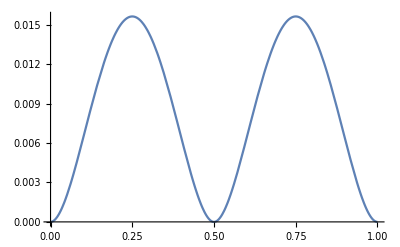

```mathematica
Plot[f,{x,0,1},GridLines->{{0,1/2,1},None}]
```

Jak widać, zera funkcji f pokrywają się z symetrycznymi równowagami Nasha. Możemy znaleźć zera tej funkcji.

```mathematica
Sort[x/.(Last/@(FindMinimum[{f,0≤x≤1},{x,#}]&/@RandomVariate[UniformDistribution[{0,1}],10]))]
```

{0.00024511,0.00025468,0.000304888,0.000335521,0.5,0.5,0.5,0.5,0.5,0.5}

Uwaga. Przeprowadźmy powyższe rozumowanie dla nieco większej gry.

```mathematica
g2=<|
"player 1"->IdentityMatrix[3],
"player 2"->IdentityMatrix[3]
|>
```

<|player 1→{{1,0,0},{0,1,0},{0,0,1}},player 2→{{1,0,0},{0,1,0},{0,0,1}}|>

```mathematica
MatrixForm/@g2
```

<|player 1→(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1),player 2→(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)|>

W pierwszej kolejności musimy zdefiniować funkcję f.

```mathematica
f=Total@Table[Max[0,getPayoff[g2,{IdentityMatrix[3]⟦k⟧,{x,y,1-x-y}}]⟦1⟧-getPayoff[g2,{{x,y,1-x-y},{x,y,1-x-y}}]⟦1⟧]^2,{k,1,3}]//Simplify
```

Max[0,x-2 x^2+y-2 x y-2 y^2]^2+Max[0,-1+3 x-2 x^2+2 y-2 x y-2 y^2]^2+Max[0,-1+2 x-2 x^2+3 y-2 x y-2 y^2]^2

```mathematica
reg=ImplicitRegion[x≥0&&y≥0&&x+y≤1,{x,y}]
```

ImplicitRegion[x≥0&&y≥0&&x+y≤1,{x,y}]

```mathematica
Show[{
Plot3D[f,{x,y}∈reg,PlotPoints->50],
Graphics3D[{LightBlue,Polygon[{{0,0,0},{1,0,0},{0,1,0}}]}]
}]
```

-Graphics3D-

```mathematica
randomPoints=RandomPoint[reg,100];
```

```mathematica
Show[{
RegionPlot[reg],
Graphics[{Point[randomPoints]}]
}]
```

-Graphics-

```mathematica
sol1=Sort[{x,y,1-x-y}/.(Last/@Table[
NMinimize[{f,{x,y}∈reg},{x,y},Method->{"NelderMead","InitialPoints"->RandomPoint[reg,1]}],{k,1,100}
])];
```

```mathematica
Graphics3D[{
{Opacity[.3],Simplex[IdentityMatrix[3]]},
{Red,PointSize[Large],Point[sol1]}
}]
```

-Graphics3D-

Jak widać wszystkie równowagi Nasha zostały znalezione.

## Automatyzcja dla gier dwuosobowych symetrycznych

Uwaga. W pierwszej kolejności chcemy mieć prostą funkcję do generowania losowych, dwuosobowych gier symetrycznych.

```mathematica
ClearAll[generateRandomSymmetricBimatrixGame]
generateRandomSymmetricBimatrixGame[𝒟_,size_]:=Module[{ret},
ret=Partition[RandomVariate[𝒟,size^2],size];
<|"player 1"->ret,"player 2"->Transpose[ret]|>
]
```

Przykładowe zastosowanie powyższej funkcji.

```mathematica
g=generateRandomSymmetricBimatrixGame[BinomialDistribution[10,1/2],3];
MatrixForm/@g
```

<|player 1→(8 | 5 | 6
5 | 7 | 4
5 | 5 | 4),player 2→(8 | 5 | 5
5 | 7 | 5
6 | 4 | 4)|>

Uwaga. W następnej kolejności chcemy zautomatyzować proces tworzenia funkcji kryterium oraz jej minimalizacji (a dokładnie szukania zer). Poniżej jest funkcja, która automatyzuje przedstawiony powyżej proces.

```mathematica
ClearAll[findSymmetricNashEquilibriaInSymmetricGame,zeroThreshold]
Options[findSymmetricNashEquilibriaInSymmetricGame]={zeroThreshold->10^(-10)};
findSymmetricNashEquilibriaInSymmetricGame[g_,numOfTest_, var_, OptionsPattern[]]:=Module[{dim,pop,popOptimVars,popsub,fFull,f,reg,preNash,nashEquilibria,errorCode=""},
dim=Dimensions[g["player 1"]]⟦1⟧;
pop=Table[var[j],{j,1,dim,1}];
popOptimVars=Most[pop];
popsub=x[dim]->1-Total@Most[pop];
fFull=Total@Table[
Max[0,getPayoff[g,{IdentityMatrix[dim]⟦k⟧,pop}]⟦1⟧-getPayoff[g,{pop,pop}]⟦1⟧]^2,
{k,1,dim,1}];
f=fFull//.popsub;
(* rzutu prostopadłego sympleksu *)
reg=ConvexHullMesh[Most/@IdentityMatrix[dim]];
preNash=Select[Table[
NMinimize[{f,popOptimVars∈reg},popOptimVars,Method->{"NelderMead","InitialPoints"->RandomPoint[reg,1]}],
{k,1,numOfTest}],(First[#]<OptionValue[zeroThreshold])&];
nashEquilibria=Null;
If[Length[preNash]>0,
nashEquilibria=Sort[(pop/.popsub)/.(Last/@preNash)];
errorCode="OK",
errorCode="no symmetric Nash equilibria found"
];
<|"error"->errorCode,"region"->reg,"full f"->fFull,"full vars"->pop,"projected f"->f,"projected vars"->popOptimVars,"vars projection"->popsub,"nash"->nashEquilibria|>
]
```

Przykład. Poniżej jest przykład zastosowania powyższej funkcji. W pierwszej kolejności chcemy wprowadzić nieco wygodniejsze formatowanie zmiennych, przy pomocy których zapisywana jest funkcja kryterium.

```mathematica
Format[x[s_]]:=Subscript[Style[x,Blue,Italic], s]
```

Definiujemy przykładową grę.

```mathematica
g=<|"player 1"->IdentityMatrix[2],"player 2"->IdentityMatrix[2]|>
```

<|player 1→{{1,0},{0,1}},player 2→{{1,0},{0,1}}|>

Następnie poszukujemy równowag symetrycznych. Zakładamy, że wykonujemy 20 testów (20 punktów, z których startujemy minimalizację), zmienna przy pomocy której zostanie zapisana funkcja kryterium to x. Przyjmujemy domyślną wartość testu czy znalezione minimum to rzeczywiście zero funkcji kryterium, które jest ustawione na wartość 10^-10.

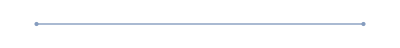
<|error→OK,region→-Graphics-,full f→Max[0,x_1-x_1^2-x_2^2]^2+Max[0,-x_1^2+x_2-x_2^2]^2,full vars→{x_1,x_2},projected f→Max[0,1-(1-x_1)^2-x_1-x_1^2]^2+Max[0,-(1-x_1)^2+x_1-x_1^2]^2,projected vars→{x_1},vars projection→x_2→1-x_1,nash→{{0.5,0.5},{0.5,0.5},{0.5,0.5},{0.5,0.5},{0.5,0.5},{0.5,0.5},{0.5,0.5},{0.5,0.5},{0.5,0.5},{1.,1.32082×10^-8},{1.,7.45065×10^-9},{1.,5.14722×10^-10},{1.,4.2329×10^-10},{1.,1.14×10^-10},{1.,1.0636×10^-10},{1.,5.56942×10^-11},{1.,5.45543×10^-11},{1.,1.66456×10^-11},{1.,-4.14463×10^-8},{1.,-1.99311×10^-7}}|>

```mathematica
sol=findSymmetricNashEquilibriaInSymmetricGame[g,20,x]
```

Możemy relatywnie łatwo przedstawić wizualizację powyższego obliczenia.

```mathematica
Keys[sol]
```

{region,full f,full vars,projected f,projected vars,nash}

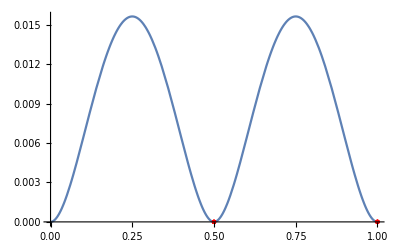

```mathematica
Plot[
sol["projected f"],sol["projected vars"]∈sol["region"],
Epilog->{PointSize[Medium],Red,Point[({First[#],0})&/@sol["nash"]]}
]
```

Przykład. Zastosowanie powyższej funkcji do losowej gry symetrycznej z dwoma graczami dwoma akcjami.

```mathematica
g=generateRandomSymmetricBimatrixGame[BinomialDistribution[10,1/2],2];
MatrixForm/@g
```

<|player 1→(4 | 4
7 | 3),player 2→(4 | 7
4 | 3)|>

Następnie poszukujemy równowag symetrycznych. Zakładamy, że wykonujemy 20 testów (20 punktów, z których startujemy minimalizację), zmienna przy pomocy której zostanie zapisana funkcja kryterium to x. Przyjmujemy domyślną wartość testu czy znalezione minimum to rzeczywiście zero funkcji kryterium, które jest ustawione na wartość 10^-10.

```mathematica
sol=findSymmetricNashEquilibriaInSymmetricGame[g,20,x]
```

<|error→OK,region→-Graphics-,full f→Max[0,7 x_1-4 x_1^2+3 x_2-11 x_1 x_2-3 x_2^2]^2+Max[0,4 x_1-4 x_1^2+4 x_2-11 x_1 x_2-3 x_2^2]^2,full vars→{x_1,x_2},projected f→Max[0,4 (1-x_1)-3 (1-x_1)^2+4 x_1-11 (1-x_1) x_1-4 x_1^2]^2+Max[0,3 (1-x_1)-3 (1-x_1)^2+7 x_1-11 (1-x_1) x_1-4 x_1^2]^2,projected vars→{x_1},vars projection→x_2→1-x_1,nash→{{0.25,0.75},{0.25,0.75},{0.25,0.75},{0.25,0.75},{0.25,0.75},{0.25,0.75},{0.25,0.75},{0.25,0.75},{0.25,0.75},{0.25,0.75},{0.25,0.75},{0.25,0.75},{0.25,0.75},{0.25,0.75},{0.25,0.75},{0.25,0.75},{0.25,0.75},{0.25,0.75},{0.25,0.75},{0.25,0.75}}|>

Możemy relatywnie łatwo przedstawić wizualizację powyższego obliczenia.

```mathematica
Keys[sol]
```

{error,region,full f,full vars,projected f,projected vars,nash}

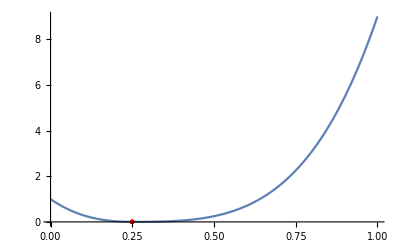

```mathematica
If[sol["error"]=="OK",
Plot[sol["projected f"],sol["projected vars"]∈sol["region"],
Epilog->{PointSize[Medium],Red,Point[({First[#],0})&/@sol["nash"]]}],
Plot[sol["projected f"],sol["projected vars"]∈sol["region"]]
]
```

W wielu przypadkach, w takiej grze nie będzie istniała symetryczna równowaga Nash w strategiach czystych (ale oczywiście musi istnieć równowaga w akcjach — strategiach czystych zgodnie z powyższymi twierdzeniami).

Przykład. Powyższa funkcja działa dla dowolnych symetryczny gier z dwoma graczami. Przykładowa gra, którą rozważaliśmy już powyżej.

```mathematica
g=<|"player 1"->DiagonalMatrix[{1,2,1}],"player 2"->DiagonalMatrix[{1,2,1}]|>;
MatrixForm/@g
```

<|player 1→(1 | 0 | 0
0 | 2 | 0
0 | 0 | 1),player 2→(1 | 0 | 0
0 | 2 | 0
0 | 0 | 1)|>

Następnie poszukujemy równowag symetrycznych. Zakładamy, że wykonujemy 20 testów (20 punktów, z których startujemy minimalizację), zmienna przy pomocy której zostanie zapisana funkcja kryterium to x. Przyjmujemy domyślną wartość testu czy znalezione minimum to rzeczywiście zero funkcji kryterium, które jest ustawione na wartość 10^-10.

```mathematica
sol=findSymmetricNashEquilibriaInSymmetricGame[g,200,x,zeroThreshold->1/100];
```

```mathematica
Sort[DeleteDuplicates[Round[sol["nash"],0.01]]]//Grid
```

0. | 0. | 1.
0. | 0.33 | 0.67
0. | 1. | 0.
0.4 | 0.2 | 0.4
0.5 | 0. | 0.5
1. | 0. | 0.

Możemy relatywnie łatwo przedstawić wizualizację powyższego obliczenia.

```mathematica
Show[{
Plot3D[sol["projected f"],Evaluate[sol["projected vars"]∈sol["region"]],PlotPoints->50,PlotStyle->Directive[Opacity[.5]],MeshFunctions->{#3&}],
Graphics3D[{Red,PointSize[Large],Point[sol["nash"]/.{x_,y_,_}->{x,y,0}]}]
}]
```

-Graphics3D-

Jak widać, nie zawsze jesteśmy w stanie znaleźć wszystkie równowagi Nasha nawet w relatywnie prostych grach. Tak czy inaczej powyższa wizualizacja nie jest optymalna dla gier symetrycznych, bo traci się w niej symetrię. Zdecydowanie lepiej jest zaproponować nieco inny rzut (faktycznie to rzut prostopadły ale w innej bazie). Poniżej jest taka nieco inna wizualizacja.

```mathematica
ClearAll[visualizeGame4]
visualizeGame4[sol_]:=Module[{trans,invtrans,projectedSimplex,projectedSimplex3D,figStrategies,y,h,nash,fignash},
trans=Transpose[{
Normalize[{0,1,0}-{1,0,0}],
Normalize[{0,0,1}-{1,1,1}/3],
Normalize[{1,1,1}]
}];
invtrans=Inverse[trans];
projectedSimplex=
ConvexHullMesh[Most/@{
invtrans.{1,0,0},
invtrans.{0,1,0},
invtrans.{0,0,1}
}];
projectedSimplex3D=ConvexHullMesh[(Append[Most[#],0])&/@({
invtrans.{1,0,0},
invtrans.{0,1,0},
invtrans.{0,0,1}
})];
figStrategies=ListPointPlot3D[
Table[Callout[MeshCoordinates[projectedSimplex3D]⟦k⟧,ToString[k]],{k,1,3,1}],
PlotStyle->Directive[Opacity[.1]]
];
If[sol["error"]=="OK",
nash=(invtrans.#)&/@sol["nash"];
nash=(Append[Most[#],0])&/@nash;
fignash=ListPointPlot3D[nash,PlotStyle->Directive[Red]];
];
h=sol["full f"]/.Thread[sol["full vars"]->trans.{y[1],y[2],1/Sqrt[3]}];
If[sol["error"]=="OK",
Show[{
Plot3D[h,{y[1],y[2]}∈projectedSimplex,PlotPoints->50,MeshFunctions->{#3&},PlotStyle->Directive[Opacity[.5],PointSize[Large]]],
Graphics3D[{Opacity[.2],projectedSimplex3D}],
figStrategies,
fignash
}],
Show[{
Plot3D[h,{y[1],y[2]}∈projectedSimplex,PlotPoints->50,MeshFunctions->{#3&},PlotStyle->Directive[Opacity[.5],PointSize[Large]]],
Graphics3D[{Opacity[.2],projectedSimplex3D}],
figStrategies
}]
]
]
```

```mathematica
visualizeGame4[sol]
```

-Graphics3D-

Mając takie zabaweczki możemy popatrzeć na kilka losowych gier.

Przykład. Powtórzenie powyższego zadania dla losowej gry.

```mathematica
g=generateRandomSymmetricBimatrixGame[DiscreteUniformDistribution[{0,50}],3];
MatrixForm/@g
```

<|player 1→(16 | 23 | 8
8 | 13 | 13
3 | 50 | 22),player 2→(16 | 8 | 3
23 | 13 | 50
8 | 13 | 22)|>

```mathematica
sol=findSymmetricNashEquilibriaInSymmetricGame[g,200,x,zeroThreshold->1/100];
```

```mathematica
Grid[DeleteDuplicates@Round[sol["nash"],0.01],Frame->All,Spacings->{1, 1}]
```

0. | 0. | 1.
0.52 | 0. | 0.48
1. | 0. | 0.

```mathematica
visualizeGame4[sol]
```

-Graphics3D-